```mathematica
A=800000;
a=80;
b=0.0007;
λ0=512;
js={60,100,120,140,180};
surf=Function[{x,y},A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((y-512)^2+a^2)(*A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((y-512)^2+a^2)*)(*A(Exp[-b(j-240)^2]+Exp[-b(j-240-100)^2])/((u-λ0)^2+a^2)*)];
height=Function[x,A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((λ0-512)^2+a^2)(*A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((λ0-512)^2+a^2)*)](*A(Exp[-b(#-240)^2]+Exp[-b(#-240-100)^2])/(2 a^2)*)(*Half height at position j, same as surf but without (u-λ0)^2*);
(*js={200,270,250,300,350,370,400};*)
```

```mathematica
plot1=ParametricPlot3D[
Table[{j,u,surf[j,u]},{j,js}],{u,0,1024},
Axes->True,
AxesStyle->Thick,
Boxed->False,
AxesLabel->Table[Style[i,Blue,Bold,10],{i,{"x","y","z"}}],
AxesStyle->Thick
,AxesOrigin->{0,0,0}
,PlotRange->{{0,256},{0,1024},{0,130}}
,ViewPoint->{27,30,10}
,ViewVertical->{0,0,9}
,ImageSize->Large
(*,AspectRatio->0.7*)]
```

-Graphics3D-

```mathematica
Δλ=Text[Style["Δλ",Bold,Red,20],{Last[js],λ0,height[Last[js]]/2-15}];
xlabel=Text[Style["x-coordinate\n[px]",Bold,Red,20],{256,0,0}];
ylabel=Text[Style["λ [nm]",Bold,Red,20],{0,1024,0}];
zlabel=Text[Style["Intensity",Bold,Red,20],{0,0,130}];
```

```mathematica
ω=0.015;(*arrow size*)
arrows=Table[
{Arrowheads[{-ω,ω}],
Arrow[{{j,λ0-a,height[j]/2},{j,λ0+a,height[j]/2}}]},
{j,js}
];
```

```mathematica
plot1=Show[{
Graphics3D[xlabel],
Graphics3D[ylabel],
Graphics3D[zlabel],
Graphics3D[arrows],
Graphics3D[Δλ],
plot1
},
Axes->True,
AxesStyle->Thick,
Boxed->False
,Ticks->{{512,256},None,None}
,AxesOrigin->{0,0,0}
,PlotRange->{{0,256},{0,1024},{0,130}}
,ViewPoint->{10,40,10}
,ViewVertical->{0,0,9}
,ImageSize->Large
,FaceGrids->{{0,0,-1}}
,FaceGridsStyle->Directive[Black]]
```

-Graphics3D-

For a lorentzian of the form used here, f(x)=1/((x-X)^2+a^2):
The half maximum is at x→X-a, x→X+a, i.e., fwhm =2a.
f(X-a)=f(X+a)=1/(2 a^2).

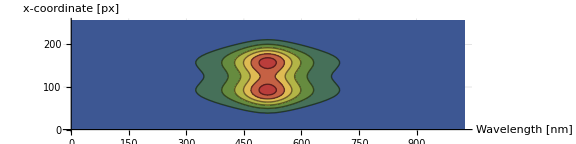

```mathematica
r=120;
b=0.0007;
plot2=ContourPlot[surf[y,x],{x,0,1024},{y,0,256},
PlotRange->Full,
ColorFunction->"DarkRainbow",
AspectRatio->1/4,
Axes->True,
AxesLabel->{"Wavelength [nm]","x-coordinate\n[px]"},
GridLines->Automatic,
Frame->False,
ImageSize->Large]
```

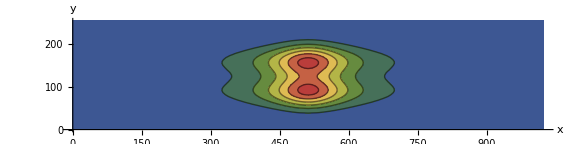
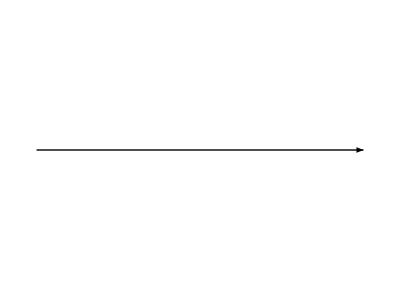
-Graphics- | Domain | -Graphics- | -Graphics3D-

```mathematica
Grid[{{
plot2
,"Domain"
,Graphics[{Arrowheads[1/2],Arrow[{{0,0},{1,0}}]}]
,plot1
}}
]
```

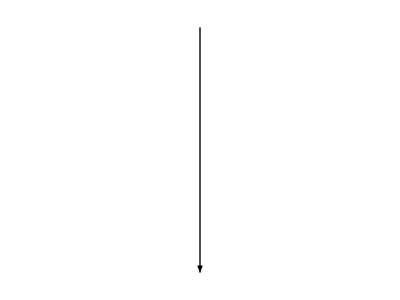
-Graphics-
-Graphics-
-Graphics3D-

```mathematica
Grid[{
{plot2},
{Graphics[{Arrowheads[1/2],Arrow[{{0,3},{0,0}}]}]},
{plot1}
}]
```